```mathematica
Get["SurfaceOfRevolution.m"]
```

General::obspkg: "Graphics`SurfaceOfRevolution`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
bb={{1/2,764},{3/2,1305},{5/2,1560},{7/2,1726},{9/2,1751},{11/2,1605},{13/2,1571},{15/2,1631},{17/2,1873},{19/2,2012},{21/2,1916},{23/2,1753},{25/2,1962},{27/2,1758},{29/2,1699},{31/2,1130}};
```

```mathematica
Export["dat.dat",dat]
```

dat.dat

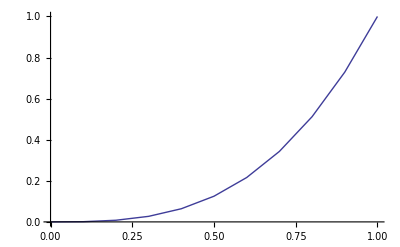

```mathematica
ListLinePlot[datorig]
```

```mathematica
dat=Table[{n,n^3,n^4},{n,0,1,.1}]
```

```mathematica
datorig=Table[{n,n^3},{n,0,1,.1}]
```

{{0.,0.},{0.1,0.001},{0.2,0.008},{0.3,0.027},{0.4,0.064},{0.5,0.125},{0.6,0.216},{0.7,0.343},{0.8,0.512},{0.9,0.729},{1.,1.}}

```mathematica
Length[datorig]
```

11

```mathematica
dat2 = Table[{dat[[i,1]],dat[[i,2]]},{i,1,Length[dat]}]
```

{{0.,0.},{0.1,0.001},{0.2,0.008},{0.3,0.027},{0.4,0.064},{0.5,0.125},{0.6,0.216},{0.7,0.343},{0.8,0.512},{0.9,0.729},{1.,1.}}

```mathematica
dat[[1,1]]
```

0.

```mathematica
dat2 = {dat[[All,1]],dat[[All,2]]}
```

{{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.},{0.,0.001,0.008,0.027,0.064,0.125,0.216,0.343,0.512,0.729,1.}}

```mathematica
qq=ListSurfaceOfRevolution[bb,RevolutionAxis->{1,0,0},PlotRange->All,BoxRatios->{2,1,1}]
```

-Graphics3D-

```mathematica
Export["tmp.pdf",qq]
```

tmp.pdf

```mathematica
$Packages
```

{ResourceLocator`,DocumentationSearch`,Utilities`FilterOptions`,Graphics`SurfaceOfRevolution`,JLink`,PacletManager`,WebServices`,System`,Global`}

```mathematica
test =Import["~/Documents/Davis/2009Spring/research/animation/data.txt","Table"];
```

```mathematica
testdat = Table[{ToExpression[test[[1,i+5]]],test[[2,i+5]]},{i,1,16}]
```

{{1/2,764},{3/2,1305},{5/2,1560},{7/2,1726},{9/2,1751},{11/2,1605},{13/2,1571},{15/2,1631},{17/2,1873},{19/2,2012},{21/2,1916},{23/2,1753},{25/2,1962},{27/2,1758},{29/2,1699},{31/2,1130}}

```mathematica
N[ToExpression[testdat[[1,1]]]]
```

0.5

```mathematica
N[1/2]
```

0.5

```mathematica
bb
```

{{1/2,764},{3/2,1305},{5/2,1560},{7/2,1726},{9/2,1751},{11/2,1605},{13/2,1571},{15/2,1631},{17/2,1873},{19/2,2012},{21/2,1916},{23/2,1753},{25/2,1962},{27/2,1758},{29/2,1699},{31/2,1130}}

```mathematica
qq=ListSurfaceOfRevolution[testdat,RevolutionAxis->{1,0,0},PlotRange->All,BoxRatios->{2,1,1}]
```

-Graphics3D-

```mathematica
thedata =Import["~/Documents/Davis/2009Spring/research/cdt/S2-pbc-T32_V8000_eps0.02_kz1.0_kt0.81_sweeps1to10000.movdat","Table"];
```

```mathematica
timesteps = Table[i/2,{i,1,64,2}]
```

{1/2,3/2,5/2,7/2,9/2,11/2,13/2,15/2,17/2,19/2,21/2,23/2,25/2,27/2,29/2,31/2,33/2,35/2,37/2,39/2,41/2,43/2,45/2,47/2,49/2,51/2,53/2,55/2,57/2,59/2,61/2,63/2}

```mathematica
Length[timesteps]
```

32

```mathematica
thedata[[1,5]]
```

300

```mathematica
anim=Animate[
ListSurfaceOfRevolution[
Table[{timesteps[[i]],thedata[[j,i]]},{i,1,Length[timesteps],1}],RevolutionAxis->{1,0,0},PlotRange->{{1/2,63/2},{-5500,5500},{-5500,5500}},BoxRatios->{3,1,1}
],
{j,1,Length[thedata],1}]
```

```mathematica
Export["test.swf",anim,"ControlAppearance"->None]
```

test.swf

```mathematica
$ExportFormats
```

{3DS,ACO,AIFF,AU,AVI,Base64,Binary,Bit,BMP,Byte,BYU,BZIP2,CDF,Character16,Character8,Complex128,Complex256,Complex64,CSV,DICOM,DIF,DXF,EPS,ExpressionML,FASTA,FITS,FLAC,FLV,GIF,Graph6,GZIP,HarwellBoeing,HDF,HDF5,HTML,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,JPEG,JPEG2000,JVX,List,LWO,MAT,MathML,Maya,MGF,MIDI,MOL,MTX,MX,NB,NOFF,OBJ,OFF,Package,PBM,PCX,PDF,PGM,PICT,PLY,PNG,PNM,POV,PPM,PXR,RawBitmap,Real128,Real32,Real64,RIB,RTF,SCT,SND,Sparse6,STL,String,SVG,SWF,Table,TAR,TerminatedString,TeX,Text,TGA,TIFF,TSV,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,UUE,VRML,WAV,Wave64,WDX,X3D,XBM,XHTML,XHTMLMathML,XLS,XML,XYZ,ZIP,ZPR}